## Landau Wave Function with Symmetric Gauge

## Parabolic Electron E_(k⃗)=ℏ^2/(2m)(k⃗)^2

#### LL Wavefunction (N=(n+m)/2, m)

```mathematica
ClearAll["Global`*"]
Clear[n,m,x0,y0]
{Subscript[l, B]}={26/10}; (* Here, m should be non-negative *)
β=Subscript[l, B]/(√2); 
Cnm[n_,m_,x0_,y0_]=(-1)^((n-m)/2)/(√π)√((((n-m)/2)!)/(((n+m)/2)!))β^(m+1)LaguerreL[(n-m)/2,m,β^2((x-x0)^2+(y-y0)^2)]Exp[-β^2((x-x0)^2+(y-y0)^2)/2];
Subscript[ψ, s][n_,m_,x0_,y0_] = Cnm[n,m,x0,y0] ((x-x0)-ⅈ (y-y0))^m;
ψ[n_,m_,x0_,y0_] = Cnm[n,m,x0,y0] ((x-x0)+ⅈ (y-y0))^m; 
ρ[n_,m_,x0_,y0_] =Subscript[ψ, s][n,m,x0,y0] ψ[n,m,x0,y0] ;
```

##### check the normalization

```mathematica
range=2;
figLandauWaveFun1=Plot3D[ρ[3, -3, 0, 0],{x,-range,range},{y,-range,range},
	                                            PlotRange->All,PlotPoints->100,PlotStyle->{Directive[Red,Opacity[0.6]]}
	                                           ];
figLandauWaveFun2=Plot3D[ρ[4, -4, 0, 0],{x,-range,range},{y,-range,range},
	                                            PlotRange->All,PlotPoints->100,PlotStyle->{Directive[Blue,Opacity[0.4]]}
	                                           ];
Show[figLandauWaveFun1,figLandauWaveFun2]
```

-Graphics3D-

0.939986

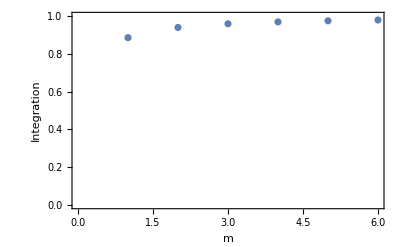

```mathematica
ψ1[n_,m_,x0_,y0_] = Cnm[n,m,x0,y0] ((x-x0)^2+ (y-y0)^2)^(m/2); 
Mmax=5;dm=1;
mx=Range[0,Mmax];
Integrate[ψ1[1,-1,0,0]ψ1[1+dm,-(1+dm),0,0], {x, -∞, ∞}, {y, -∞, ∞}]//N
ListPlot[Integrate[ψ1[mx,-mx,0,0]ψ1[mx+dm,-(mx+dm),0,0], {x, -∞, ∞}, {y, -∞, ∞}]//N,
		AxesLabel->{m,Integration},Frame->True,PlotRange->{{0,Mmax+1},{0,1}}]
```

## Dirac Electron E_(k⃗)=ℏ v⃗·k⃗

```mathematica
H1={{0, 0, km, kz}, {0, 0, kz, -kp}, {kp, kz, 0, 0}, {kz, -km, 0, 0}};
UU={{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}};
UU.H1.Inverse[UU]//MatrixForm
UU.{{1}, {2}, {3}, {4}}//MatrixForm
```

(0 | km | 0 | kz
kp | 0 | kz | 0
0 | kz | 0 | -kp
kz | 0 | -km | 0)

(1
3
2
4)